# Rate of NS-NS events

## Schechter Function

```mathematica
b=1;
phi=22.4*10^(-4);
mchar=11.20;
alph=-1.19;
```

```mathematica
schecter[M_]:=b*phi*Log[10]*10^((b*(M-mchar))*(1+alph))*Exp[-10^(b*(M-mchar))]
```

### Number of galaxies in Gpc^3

```mathematica
numGalaxy=10^9*NIntegrate[schecter[M],{M,8,12}]
```

3.42186×10^7

Stellar mass in 1 Gpc^3

```mathematica
numMass=10^9*NIntegrate[10^M*schecter[M],{M,6,12}]
```

4.08927×10^17

```mathematica
rateRet=(1/111600)*(1/((1.382*10^10)-(1.003*10^9)))
```

6.99116×10^-16

```mathematica
rateRet*numMass
```

285.888

```mathematica
imf[m_]:=m^(-2.3)
```

```mathematica
numStarperGal=10^10*NIntegrate[imf[m],{m,0.5,Infinity}]
```

1.89407×10^10

```mathematica
Assuming all stars formed at same time, that they live forever,that there are 10^10 stars in Milky Way.
```

```mathematica
c=10^.1d10
```

## Star Formation Rate Functions

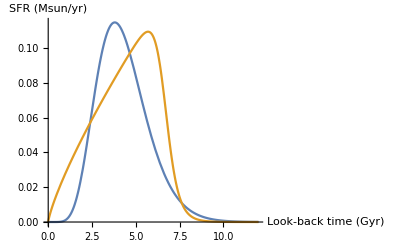

0.401038

0.49081

```mathematica
d1=7.6;
tau1=0.5;
psi1[t_]:=t^d1*Exp[-t/tau1];
BA=18.6;$Failed
CA=0.8;
tauA=6.7;
psiA[t_]:=((t/tauA)^BA+(t/tauA)^(-CA))^(-1);
Plot[{0.009*psi1[t],0.13*psiA[t]},{t,0,12},AxesLabel->{"Look-back time (Gyr)","SFR (Msun/yr)"}]
Integrate[0.009psi1[t],{t,0,Infinity}]
Integrate[0.13psiA[t],{t,0,Infinity}]
```

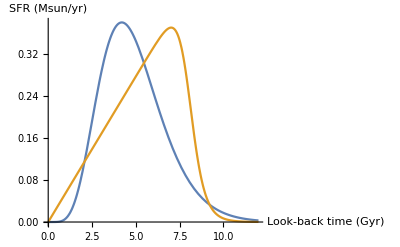

1.66026

1.85052

```mathematica
d2=6.0;
tau2=0.7;
psi2[t_]:=t^d2*Exp[-t/tau2];
BB=19.8;
CB=1.0;
tauB=8.1;
psiB[t_]:=((t/tauB)^BB+(t/tauB)^(-CB))^(-1);
Plot[{0.028*psi2[t],0.45*psiB[t]},{t,0,12},AxesLabel->{"Look-back time (Gyr)","SFR (Msun/yr)"}]
Integrate[0.028psi2[t],{t,0,Infinity}]
Integrate[0.45psiB[t],{t,0,Infinity}]
```

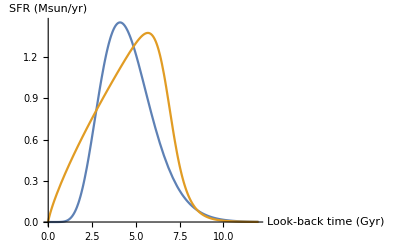

5.27183

6.67797

```mathematica
d3=8.2;
tau3=0.5;
psi3[t_]:=t^d3*Exp[-t/tau3];
BC=14.0;
CC=0.8;
tauC=6.9;
psiC[t_]:=((t/tauC)^BC+(t/tauC)^(-CC))^(-1);
Plot[{0.050*psi3[t],1.70*psiC[t]},{t,0,12},AxesLabel->{"Look-back time (Gyr)","SFR (Msun/yr)"}]
Integrate[0.050*psi3[t],{t,0,Infinity}]
Integrate[1.7*psiC[t],{t,0,Infinity}]
```

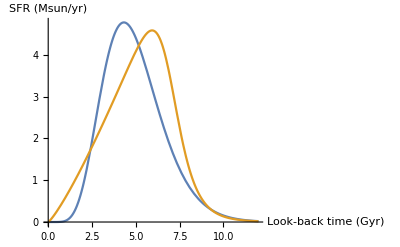

19.4959

21.424

```mathematica
d4=7.2;
tau4=0.6;
psi4[t_]:=t^d4*Exp[-t/tau4];
BD=11.2;
CD=1.2;
tauD=7.1;
psiD[t_]:=((t/tauD)^BD+(t/tauD)^(-CD))^(-1);
Plot[{0.17*psi4[t],6.3*psiD[t]},{t,0,12},AxesLabel->{"Look-back time (Gyr)","SFR (Msun/yr)"}]
Integrate[0.17*psi4[t],{t,0,Infinity}]
Integrate[6.3*psiD[t],{t,0,Infinity}]
```

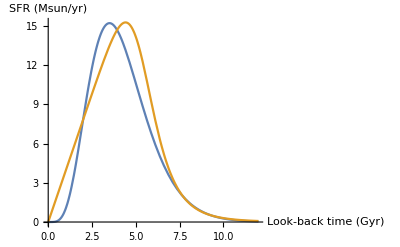

60.7069

67.7426

```mathematica
d5=5.0;
tau5=0.7;
psi5[t_]:=t^d5*Exp[-t/tau5];
BE=7.4;
CE=1.0;
tauE=5.6;
psiE[t_]:=((t/tauE)^BE+(t/tauE)^(-CE))^(-1);
Plot[{4.3*psi5[t],22*psiE[t]},{t,0,12},AxesLabel->{"Look-back time (Gyr)","SFR (Msun/yr)"}]
Integrate[4.3*psi5[t],{t,0,Infinity}]
Integrate[22*psiE[t],{t,0,Infinity}]
```